```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
```

```mathematica
A = 1.0*Import["data/pressureMatrix.txt","Data"];
B = 1.0*Import["data/rightPart.txt","Data"];
U = Table[Subscript[u, i],{i,1,Length[A]}];
matrixSize = √Length[A];
borderLength =1.0;
```

```mathematica
resGauss = 1.0*Flatten[Import["result/solution.txt","Data"]];
(*
mp = 1.0*Import["data/matrixPressureForSol.txt","Table"];
vp = 1.0*Import["data/rightPart.txt","Table"];0
resGauss = Flatten[LinearSolve[mp,vp]];
*)
```

```mathematica
matrixResultGauss = Table[0,{i,1,matrixSize},{j,1,matrixSize}];
For[i=0,i< matrixSize,i++,{
For[j=1,j≤ matrixSize,j++,{
matrixResultGauss[[i+1]][[j]]=resGauss[[i*matrixSize+j]];
}]
}]
diagram3DGauss= Table[{0,0,0},{i,1,matrixSize},{j,1,matrixSize}];
xOrigin = 0.0;hx =borderLength/ (matrixSize-1);
yOrigin = 0.0;hy =borderLength / (matrixSize-1);
For[i=1,i≤ matrixSize,i++,{
For[j=1,j<=matrixSize,j++,{
diagram3DGauss[[i]][[j]][[1]]=xOrigin + hx *( i-1);
diagram3DGauss[[i]][[j]][[2]]=yOrigin + hy * (j - 1);
diagram3DGauss[[i]][[j]][[3]]=matrixResultGauss[[i]][[j]];
}]
}]
```

-Graphics3D-

-Graphics3D-

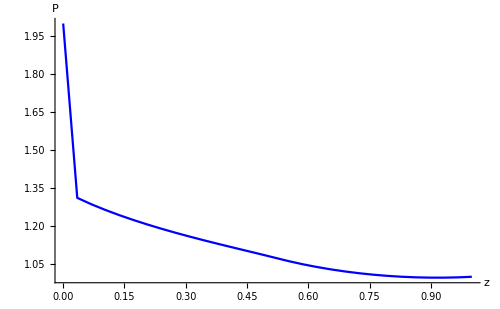

```mathematica
(*3d graph*)
listPlotDiagram = ListPointPlot3D[diagram3DGauss,
PlotStyle->PointSize[0.02],
ViewPoint->{-0.790,3.054,0.947},
PlotRange->All,AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],Style["s",16,Italic,Black,FontFamily->"Times"],Style["P",16,Black,Italic,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,Arrowheads[{0.0,0.03}],FontFamily->"Times"],
AxesStyle->Thick,
ImageSize->500,
Lighting->{{"Ambient", LightBlue}}];

(*surface*)
surface=Plot3D[1.0+0.2*s,{z,0.0,borderLength},{s,0.0,borderLength},AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],Style["s",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,
Background->White,
BoundaryStyle->Thick,
Filling->Bottom,
ImageSize->500,
FillingStyle-> LightBlue,
Lighting->{{"Ambient", LightBlue}}, ViewPoint->{3.07559,0.7744956,0.888102}];

(*axes labels for simple search rotation*)
axesOrigin1 = Graphics3D[{PointSize[0.05],
Point[{0,0,0},VertexColors->Red]}];
axesOrigin2 = Graphics3D[{PointSize[0.05],
Point[{0.02,0,0},VertexColors->Blue]}];
axesOrigin3 = Graphics3D[{PointSize[0.05],
Point[{0,0.02,0},VertexColors->Green]}];

(*proection*)
colomn =matrixSize/2+1;
graphT2 = Table[{0,0},{i,1,matrixSize}];
For[i=1,i≤matrixSize,i++,{
graphT2[[i]][[1]]=diagram3DGauss[[i]][[colomn]][[1]];
graphT2[[i]][[2]]=diagram3DGauss[[i]][[colomn]][[3]];
}];
proec = ListLinePlot[graphT2,
PlotRange->All,
GridLines->Full,
ImageSize->500,
PlotStyle->{Blue},
AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],Style["P",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,
PlotStyle->{Darker[Red,0.4],Thick}];
Show[listPlotDiagram]
Show[surface]
Show[proec,
PlotRange->All]
```

```mathematica
(*step = 8;
errorMatrix = Table[0,{i,1,7},{j,1,7}];
c1 = 0; c2 = 0;
For[i=1+step,i≤ matrixSize - step,i+=step,{
c1++;c2=0;
For[j=1+step,j≤ matrixSize - step,j+= step,{
c2++;
errorMatrix[[c2]][[c1]] = matrixResultGauss[[j]][[i]];
}]
}]
Export["result/errorMatrix65.txt",errorMatrix,"Table"];

err1 = Import["result/errorMatrix17.txt","Data"];
err2 = Import["result/errorMatrix33.txt","Data"];
err3 = Import["result/errorMatrix65.txt","Data"];

MatrixForm[err1-err2];
MatrixForm[err2-err3];
MatrixForm[err3-err1];
Max[Abs[err1-err2]]
200.
Max[Abs[err2-err3]]
175400.*)
```

```mathematica
err1 = Import["result/graph16.txt","Data"];
err2 = Import["result/graph32.txt","Data"];
err3 = Import["result/graph64.txt","Data"];
ListLinePlot[{err1,err2,err3},PlotStyle->{Red, Blue, Green},
GridLines->Full,
ImageSize->500,
PlotStyle->Blue,
PlotStyle->{Darker[Red,0.4],Thick},
PlotRange->All,
AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],Style["p",16,Italic,Black,FontFamily->"Times"]},AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick]
```

Import::nffil: File result/graph16.txt not found during Import.

Import::nffil: File result/graph32.txt not found during Import.

Import::nffil: File result/graph64.txt not found during Import.

-Graphics-

```mathematica
mA1={{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,-1,0,0,0},{0,-1,0,-1,4,-1,0,-1,0},{0,0,0,1,-1,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}};
```

```mathematica
MatrixRank[mA1]
```

9

```mathematica
LinearSolve[mA1, {1,1,1,0,0,0,2,2,2}]
```

{1,1,1,1/2,1,1/2,2,2,2}

```mathematica
mA2={{1 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0 ,1 ,0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0 ,0 ,0 ,1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{
0, 0, 0, 0, 1, 0, 0,-1, 0, 0, 0, 0, 0, 0, 0, 0},{0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0, 0, 0, 0, 0, 0},{0, 0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1,-1,-1, 1, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0,-1, 0, 0, 0, 0},{0 ,0 ,0 ,0 ,0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0, 0},{0 ,0 ,0 ,0 ,0, 0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0},{0, 0, 0, 0, 0, 0, 0, 0, 1,-1,-1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0},{0, 0, 0, 0, 0, 0 ,0, 0, 0, 0, 0, 0, 0, 1, 0, 0},{
0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,1, 0},{0, 0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0, 0, 0, 1}};
MatrixRank[mA2]
```

16

```mathematica
LinearSolve[mA2,{1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 2, 2, 2, 2}]
```

{1,1,1,1,4/3,4/3,4/3,4/3,5/3,5/3,5/3,5/3,2,2,2,2}

```mathematica
MatrixForm[{{1 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0 ,1 ,0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0 ,0 ,0 ,1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{
0, 0, 0, 0, 1, 0, 0,-1, 0, 0, 0, 0, 0, 0, 0, 0},{0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0, 0, 0, 0, 0, 0},{0, 0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1,-1,-1, 1, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0,-1, 0, 0, 0, 0},{0 ,0 ,0 ,0 ,0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0, 0},{0 ,0 ,0 ,0 ,0, 0,-1, 0, 0,-1, 4,-1, 0, 0,-1, 0},{0, 0, 0, 0, 0, 0, 0, 0, 1,-1,-1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0},{0, 0, 0, 0, 0, 0 ,0, 0, 0, 0, 0, 0, 0, 1, 0, 0},{
0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,1, 0},{0, 0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0, 0, 0, 1}}]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
mA = {
{1, 0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0 ,0 ,0 ,0 ,0 ,0 ,0 ,0, 0, 0 ,0 ,0 ,0},
{0 ,1, 0 ,0, 0 ,0 ,0 ,0 ,0 ,0, 0, 0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0, 0, 0 ,0 ,0 ,0},
{0 ,0, 1, 0, 0, 0, 0 ,0 ,0 ,0 ,0, 0, 0, 0, 0 ,0, 0, 0, 0 ,0, 0 ,0 ,0 ,0 ,0},
{0 ,0, 0, 1 ,0, 0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0, 0, 0, 0, 0 ,0 ,0},
{0, 0 ,0, 0, 1, 0, 0, 0, 0 ,0 ,0 ,0 ,0, 0, 0, 0, 0, 0 ,0, 0, 0 ,0 ,0 ,0 ,0},
{0 ,0, 0, 0, 0 ,1, 0, 0, 0,-1, 0, 0, 0, 0, 0, 0 ,0 ,0, 0, 0, 0 ,0, 0, 0, 0},
{0,-1 ,0 ,0 ,0,-1, 4,-1 ,0 ,0 ,0,-1 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0 ,0, 0, 0 ,0},
{0 ,0,-1, 0, 0 ,0,-1, 4,-1, 0, 0, 0,-1, 0, 0, 0 ,0 ,0, 0, 0, 0, 0, 0, 0, 0},
{0 ,0, 0,-1, 0 ,0 ,0,-1, 4,-1, 0, 0, 0,-1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
{0 ,0, 0, 0, 0 ,1,-1, 0,-1, 1, 0, 0, 0, 0 ,0, 0 ,0, 0, 0, 0, 0, 0, 0, 0, 0},
{0 ,0, 0, 0, 0 ,0, 0, 0, 0, 0, 1, 0, 0, 0,-1 ,0, 0, 0, 0, 0, 0, 0, 0 ,0 ,0},
{0 ,0 ,0, 0, 0 ,0,-1, 0, 0, 0,-1, 4,-1, 0, 0 ,0,-1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 0 ,0 ,0, 0 ,0 ,0,-1 ,0 ,0 ,0,-1, 4,-1, 0, 0, 0,-1, 0, 0, 0, 0 ,0 ,0, 0},
{0, 0, 0, 0 ,0 ,0, 0, 0,-1, 0, 0, 0,-1, 4,-1, 0 ,0 ,0,-1, 0, 0, 0, 0, 0, 0},
{0, 0, 0, 0, 0 ,0, 0,0, 0 ,0, 1,-1, 0,-1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 0, 0, 0 ,0, 0, 0, 0, 0, 0, 0 ,0, 0, 0 ,1 ,0 ,0, 0,-1, 0, 0, 0, 0, 0},
{0 ,0, 0 ,0 ,0, 0 ,0, 0, 0, 0, 0,-1, 0, 0 ,0,-1, 4,-1, 0, 0, 0,-1, 0, 0, 0},
{0 ,0 ,0, 0 ,0 ,0, 0, 0, 0, 0, 0, 0,-1, 0 ,0, 0,-1, 4,-1, 0, 0, 0,-1, 0, 0},
{0 ,0, 0, 0, 0 ,0 ,0 ,0, 0 ,0, 0, 0, 0,-1, 0, 0, 0,-1, 4,-1, 0, 0, 0,-1, 0},
{0 ,0 ,0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0 ,0, 0, 1,-1, 0,-1, 1, 0, 0, 0, 0, 0},
{0, 0, 0, 0 ,0, 0 ,0 ,0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},
{0, 0 ,0 ,0, 0, 0, 0, 0, 0, 0, 0, 0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0},
{0 ,0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0},
{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0 ,0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0},
{0, 0 ,0 ,0, 0, 0 ,0, 0, 0, 0 ,0, 0, 0, 0 ,0 ,0 ,0, 0, 0, 0, 0, 0, 0, 0, 1}};
```

```mathematica
MatrixForm[mA]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
mF={1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2, 2, 2, 2, 2};

LinearSolve[mA, mF]
```

{1,1,1,1,1,5/4,5/4,5/4,5/4,5/4,3/2,3/2,3/2,3/2,3/2,7/4,7/4,7/4,7/4,7/4,2,2,2,2,2}

```mathematica
MatrixRank[mA]
```

25

```mathematica
t1=Collect[Expand[(bl + dl*z)(A1+A2*s+A3*s^2+A4*s^3)(R1+R4*z)+(cl+dl*s)(A1+A2*s+A3*s^2+A4*s^3)(R2+R4*s)+(al+bl*s+cl*z+dl*s*z)R3],{z}]
```

A1 bl R1+A1 cl R2+al R3+A2 bl R1 s+A2 cl R2 s+A1 dl R2 s+bl R3 s+A1 cl R4 s+A3 bl R1 s^2+A3 cl R2 s^2+A2 dl R2 s^2+A2 cl R4 s^2+A1 dl R4 s^2+A4 bl R1 s^3+A4 cl R2 s^3+A3 dl R2 s^3+A3 cl R4 s^3+A2 dl R4 s^3+A4 dl R2 s^4+A4 cl R4 s^4+A3 dl R4 s^4+A4 dl R4 s^5+(A1 dl R1+cl R3+A1 bl R4+A2 dl R1 s+dl R3 s+A2 bl R4 s+A3 dl R1 s^2+A3 bl R4 s^2+A4 dl R1 s^3+A4 bl R4 s^3) z+(A1 dl R4+A2 dl R4 s+A3 dl R4 s^2+A4 dl R4 s^3) z^2

```mathematica
(*не зубудь в степень еще возвести*)
```

```mathematica
t2=Collect[Integrate[t1,z],z]
```

(A1 bl R1+A1 cl R2+al R3+A2 bl R1 s+A2 cl R2 s+A1 dl R2 s+bl R3 s+A1 cl R4 s+A3 bl R1 s^2+A3 cl R2 s^2+A2 dl R2 s^2+A2 cl R4 s^2+A1 dl R4 s^2+A4 bl R1 s^3+A4 cl R2 s^3+A3 dl R2 s^3+A3 cl R4 s^3+A2 dl R4 s^3+A4 dl R2 s^4+A4 cl R4 s^4+A3 dl R4 s^4+A4 dl R4 s^5) z+((A1 dl R1)/2+(cl R3)/2+(A1 bl R4)/2+1/2 A2 dl R1 s+(dl R3 s)/2+1/2 A2 bl R4 s+1/2 A3 dl R1 s^2+1/2 A3 bl R4 s^2+1/2 A4 dl R1 s^3+1/2 A4 bl R4 s^3) z^2+((A1 dl R4)/3+1/3 A2 dl R4 s+1/3 A3 dl R4 s^2+1/3 A4 dl R4 s^3) z^3

```mathematica
t3=Collect[Integrate[t2,s],s]
```

((A4 dl R2)/5+(A4 cl R4)/5+(A3 dl R4)/5) s^5 z+1/6 A4 dl R4 s^6 z+s z (A1 bl R1+A1 cl R2+al R3+1/2 (A1 dl R1+cl R3+A1 bl R4) z+1/3 A1 dl R4 z^2)+s^2 z ((A2 bl R1)/2+(A2 cl R2)/2+(A1 dl R2)/2+(bl R3)/2+(A1 cl R4)/2+1/4 (A2 dl R1+dl R3+A2 bl R4) z+1/6 A2 dl R4 z^2)+s^3 z ((A3 bl R1)/3+(A3 cl R2)/3+(A2 dl R2)/3+(A2 cl R4)/3+(A1 dl R4)/3+1/6 A3 (dl R1+bl R4) z+1/9 A3 dl R4 z^2)+s^4 z ((A4 bl R1)/4+(A4 cl R2)/4+(A3 dl R2)/4+(A3 cl R4)/4+(A2 dl R4)/4+1/8 A4 (dl R1+bl R4) z+1/12 A4 dl R4 z^2)

```mathematica
t4 = Collect[t3,{bl*R1,cl*R2,cl*R1,bl*R2,R1*dl,R2*dl,R3,R4*dl,R4*cl,R4*bl}]
```

bl R1 (A1 s z+1/2 A2 s^2 z+1/3 A3 s^3 z+1/4 A4 s^4 z)+cl R2 (A1 s z+1/2 A2 s^2 z+1/3 A3 s^3 z+1/4 A4 s^4 z)+dl R2 (1/2 A1 s^2 z+1/3 A2 s^3 z+1/4 A3 s^4 z+1/5 A4 s^5 z)+cl R4 (1/2 A1 s^2 z+1/3 A2 s^3 z+1/4 A3 s^4 z+1/5 A4 s^5 z)+R3 (al s z+1/2 bl s^2 z+1/2 cl s z^2+1/4 dl s^2 z^2)+dl R1 (1/2 A1 s z^2+1/4 A2 s^2 z^2+1/6 A3 s^3 z^2+1/8 A4 s^4 z^2)+bl R4 (1/2 A1 s z^2+1/4 A2 s^2 z^2+1/6 A3 s^3 z^2+1/8 A4 s^4 z^2)+dl R4 (1/3 A1 s^3 z+1/4 A2 s^4 z+1/5 A3 s^5 z+1/6 A4 s^6 z+1/3 A1 s z^3+1/6 A2 s^2 z^3+1/9 A3 s^3 z^3+1/12 A4 s^4 z^3)

```mathematica
FullSimplify[Solve[{ai+bi*xi+ci*yi==1,ai+bi*xj+ci*yj==0,ai+bi*xk+ci*yk==0},{ai,bi,ci}]/.xk->xi/.yj->yi]
```

{{ai→-xj/(xi-xj)+yi/(-yi+yk),bi→1/(xi-xj),ci→1/(yi-yk)}}

```mathematica
S=xj*yk-xk*yj+yj*xi-yk*xi+xk*yi-xj*yi
```

-xj yi+xk yi+xi yj-xk yj-xi yk+xj yk

```mathematica
FullSimplify[S+(xj yi-xk yi-xi yj+xk yj+xi yk-xj yk)]
```

0

```mathematica
(*New variant*)
```

```mathematica
FullSimplify[Solve[{ai+bi*xi+ci*yi+di*xi*yi==1,ai+bi*xj+ci*yj+di*xj*yj==0,ai+bi*xk+ci*yk+di*xk*yk==0,ai+bi*xm+ci*ym+di*xm*ym==0},{ai,bi,ci,di}]/.xm->xi/.ym->yk/.xj->xk/.yj->yi]
```

{{ai→(xk yk)/((xi-xk) (yi-yk)),bi→yk/((xi-xk) (-yi+yk)),ci→xk/((-xi+xk) (yi-yk)),di→1/((xi-xk) (yi-yk))}}

```mathematica
FullSimplify[Solve[{aj+bj*xi+cj*yi+dj*xi*yi==0,aj+bj*xj+cj*yj+dj*xj*yj==1,aj+bj*xk+cj*yk+dj*xk*yk==0,aj+bj*xm+cj*ym+dj*xm*ym==0},{aj,bj,cj,dj}]/.xm->xi/.ym->yk/.xj->xk/.yj->yi]
```

{{aj→(xi yk)/((xi-xk) (-yi+yk)),bj→yk/((xi-xk) (yi-yk)),cj→xi/((xi-xk) (yi-yk)),dj→1/((-xi+xk) (yi-yk))}}

```mathematica
FullSimplify[Solve[{ak+bk*xi+ck*yi+dk*xi*yi==0,ak+bk*xj+ck*yj+dk*xj*yj==0,ak+bk*xk+ck*yk+dk*xk*yk==1,ak+bk*xm+ck*ym+dk*xm*ym==0},{ak,bk,ck,dk}]/.xm->xi/.ym->yk/.xj->xk/.yj->yi]
```

{{ak→(xi yi)/((xi-xk) (yi-yk)),bk→yi/((xi-xk) (-yi+yk)),ck→xi/((xi-xk) (-yi+yk)),dk→1/((xi-xk) (yi-yk))}}

```mathematica
FullSimplify[Solve[{am+bm*xi+cm*yi+dm*xi*yi==0,am+bm*xj+cm*yj+dm*xj*yj==0,am+bm*xk+cm*yk+dm*xk*yk==0,am+bm*xm+cm*ym+dm*xm*ym==1},{am,bm,cm,dm}]/.xm->xi/.ym->yk/.xj->xk/.yj->yi]
```

{{am→(xk yi)/((-xi+xk) (yi-yk)),bm→yi/((xi-xk) (yi-yk)),cm→xk/((xi-xk) (yi-yk)),dm→1/((-xi+xk) (yi-yk))}}

```mathematica
(*upper*)
```

```mathematica
n [x_,y_]:= ((xk yk)/((xi-xk) (yi-yk)))+(yk/((xi-xk) (-yi+yk)))*x+(xk/((-xi+xk) (yi-yk)))*y+(1/((xi-xk) (yi-yk)))*x*y
```

```mathematica
FullSimplify[n[xm,ym]/.xk->xm/.yk->yj]
```

0

```mathematica
n1[x_,y_]:= ((xi yi)/((xi-xk) (yi-yk)))+(yi/((xi-xk) (-yi+yk)))*x+(xi/((xi-xk) (-yi+yk)))*y+(1/((xi-xk) (yi-yk)))*x*y
```

```mathematica
FullSimplify[n1[xm,ym]]
```

((xi-xm) (yi-ym))/((xi-xk) (yi-yk))

```mathematica
Integrate[(bl + dl*z)(A1+A2*s+A3*s^2+A4*s^3)(R1+R4*z)+(cl+dl*s)(A1+A2*s+A3*s^2+A4*s^3)(R2+R4*s)+(al+bl*s+cl*z+dl*s*z)R3,{z,zi,zj},{s,si,sm}]
```

1/60 (60 A1 cl R2 si zi+60 al R3 si zi+30 A2 cl R2 si^2 zi+30 A1 dl R2 si^2 zi+30 bl R3 si^2 zi+30 A1 cl R4 si^2 zi+20 A3 cl R2 si^3 zi+20 A2 dl R2 si^3 zi+20 A2 cl R4 si^3 zi+20 A1 dl R4 si^3 zi+15 A4 cl R2 si^4 zi+15 A3 dl R2 si^4 zi+15 A3 cl R4 si^4 zi+15 A2 dl R4 si^4 zi+12 A4 dl R2 si^5 zi+12 A4 cl R4 si^5 zi+12 A3 dl R4 si^5 zi+10 A4 dl R4 si^6 zi-60 A1 cl R2 sm zi-60 al R3 sm zi-30 A2 cl R2 sm^2 zi-30 A1 dl R2 sm^2 zi-30 bl R3 sm^2 zi-30 A1 cl R4 sm^2 zi-20 A3 cl R2 sm^3 zi-20 A2 dl R2 sm^3 zi-20 A2 cl R4 sm^3 zi-20 A1 dl R4 sm^3 zi-15 A4 cl R2 sm^4 zi-15 A3 dl R2 sm^4 zi-15 A3 cl R4 sm^4 zi-15 A2 dl R4 sm^4 zi-12 A4 dl R2 sm^5 zi-12 A4 cl R4 sm^5 zi-12 A3 dl R4 sm^5 zi-10 A4 dl R4 sm^6 zi+30 cl R3 si zi^2+15 dl R3 si^2 zi^2-30 cl R3 sm zi^2-15 dl R3 sm^2 zi^2-60 A1 cl R2 si zj-60 al R3 si zj-30 A2 cl R2 si^2 zj-30 A1 dl R2 si^2 zj-30 bl R3 si^2 zj-30 A1 cl R4 si^2 zj-20 A3 cl R2 si^3 zj-20 A2 dl R2 si^3 zj-20 A2 cl R4 si^3 zj-20 A1 dl R4 si^3 zj-15 A4 cl R2 si^4 zj-15 A3 dl R2 si^4 zj-15 A3 cl R4 si^4 zj-15 A2 dl R4 si^4 zj-12 A4 dl R2 si^5 zj-12 A4 cl R4 si^5 zj-12 A3 dl R4 si^5 zj-10 A4 dl R4 si^6 zj+60 A1 cl R2 sm zj+60 al R3 sm zj+30 A2 cl R2 sm^2 zj+30 A1 dl R2 sm^2 zj+30 bl R3 sm^2 zj+30 A1 cl R4 sm^2 zj+20 A3 cl R2 sm^3 zj+20 A2 dl R2 sm^3 zj+20 A2 cl R4 sm^3 zj+20 A1 dl R4 sm^3 zj+15 A4 cl R2 sm^4 zj+15 A3 dl R2 sm^4 zj+15 A3 cl R4 sm^4 zj+15 A2 dl R4 sm^4 zj+12 A4 dl R2 sm^5 zj+12 A4 cl R4 sm^5 zj+12 A3 dl R4 sm^5 zj+10 A4 dl R4 sm^6 zj-30 cl R3 si zj^2-15 dl R3 si^2 zj^2+30 cl R3 sm zj^2+15 dl R3 sm^2 zj^2+5/6 (4 A3 si^3+3 A4 si^4+12 A1 (si-sm)-4 A3 sm^3-3 A4 sm^4+6 A2 (si^2-sm^2)) (zi-zj) (6 bl R1+3 dl R1 (zi+zj)+3 bl R4 (zi+zj)+2 dl R4 (zi^2+zi zj+zj^2)))

```mathematica
bl R1 (1)+cl R2 (2)+dl R2 (3)+cl R4 (4)+R3 (al s z+1/2 bl s^2 z+1/2 cl s z^2+1/4 dl s^2 z^2)+dl R1 (5)+bl R4 (6)+dl R4 (7)
```

bl R1+5 dl R1+2 cl R2+3 dl R2+6 bl R4+4 cl R4+7 dl R4+R3 (al s z+1/2 bl s^2 z+1/2 cl s z^2+1/4 dl s^2 z^2)

```mathematica
Integrate[1/Cos[x]^4,x]
```

(2 Tan[x])/3+1/3 Sec[x]^2 Tan[x]